```mathematica
(*Max classical state number and system time*)
num=70;
t=10;
```

```mathematica
(*Governing matrix list and initial state list *)
GovernMatClassList=List[];
InitStateClassList=List[];
(*the exact value accordingly*)
GovernMatClassListExact=List[];
InitStateClassListExact=List[];
Do[
If[i≤17,
QCTMC=QueueInit[i,0,"A"];
GovM=GovernMat[QCTMC];
Init=Flatten[RandomInitState[QCTMC,"A"]];
AppendTo[GovernMatClassListExact,GovM];
AppendTo[InitStateClassListExact,Init];
AppendTo[GovernMatClassList,N[GovM]];
AppendTo[InitStateClassList,N[Init]];
,
QCTMC=QueueInit[i,0,"N"];
GovMNum=GovernMat[QCTMC];
Init=Flatten[RandomInitState[QCTMC]];
AppendTo[GovernMatClassList,GovMNum];
AppendTo[InitStateClassList,Init];
];
If[Mod[i,10]==0,Print[i]];
,{i,2,num}]
```

10

20

30

40

$Aborted

```mathematica
(* Exact Value *)
ExactClassList=List[];
ExactClassInitList=List[];
Do[
GovM=GovernMatClassListExact[[i-1]];
ExactRes=MatrixExp[GovM*t];
AppendTo[ExactClassList,ExactRes];
AppendTo[ExactClassInitList,ExactRes.InitStateClassListExact[[i-1]]];
Print[i];
,{i,2,15}]
```

```mathematica
ssClassTimeList=List[];
PadeClassTimeList=List[];
KryClassTimeList=List[];
ssClassErrorList=List[];
PadeClassErrorList=List[];
KryClassErrorList=List[];
Do[
NumM=GovernMatClassList[[i-1]];
ssRes=AbsoluteTiming[ExpSS[NumM*t]];
PadeRes=AbsoluteTiming[MatrixExp[NumM*t,Method->"Pade"]];
KryRes=AbsoluteTiming[MatrixExp[NumM*t,InitStateClassList[[i-1]],Method->"Krylov"]];
AppendTo[ssClassTimeList,ssRes[[1]]];
AppendTo[PadeClassTimeList,PadeRes[[1]]];
AppendTo[KryClassTimeList,KryRes[[1]]];
If[i≤15,
AppendTo[ssClassErrorList,Max[Abs[ssRes[[2]]-ExactClassList[[i-1]]]]];
AppendTo[PadeClassErrorList,Max[Abs[PadeRes[[2]]-ExactClassList[[i-1]]]]];
AppendTo[KryClassErrorList,Max[Abs[KryRes[[2]]-ExactClassInitList[[i-1]]]]];
];
Print[i];
If[Mod[i,10]==0,Print[i]];
,{i,2,num}]
```

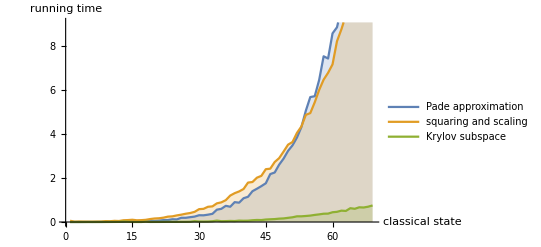

```mathematica
OverallClassTime=ListLinePlot[{PadeClassTimeList,ssClassTimeList,KryClassTimeList},Filling->Axis,PlotLegends->{"Pade approximation","squaring and scaling","Krylov subspace"},AxesLabel->{"classical state","running time"}]
```

```mathematica
Export[NotebookDirectory[]<>"EPS_figure\\OverallClassTime.eps",OverallClassTime]
```

C:\Users\mei\Desktop\Numerical methods\EPS_figure\OverallClassTime.eps

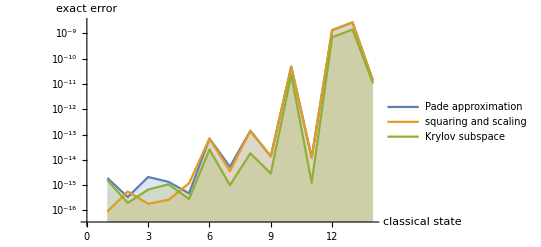

```mathematica
OverallClassAcu=ListLinePlot[{PadeClassErrorList,ssClassErrorList,KryClassErrorList},Filling->Axis,PlotLegends->{"Pade approximation","squaring and scaling","Krylov subspace"},AxesLabel->{"classical state","exact error"},ScalingFunctions->"Log"]
```

```mathematica
Export[NotebookDirectory[]<>"EPS_figure\\OverallClassAcu.eps",OverallClassAcu]
```

C:\Users\mei\Desktop\Numerical methods\EPS_figure\OverallClassAcu.eps

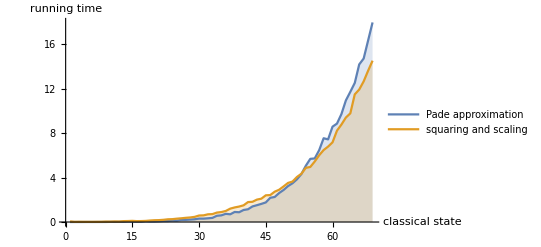

```mathematica
SSPadeClassTime=ListLinePlot[{PadeClassTimeList,ssClassTimeList},Filling->Axis,PlotLegends->{"Pade approximation","squaring and scaling"},AxesLabel->{"classical state","running time"}]
```

```mathematica
Export[NotebookDirectory[]<>"EPS_figure\\SSPadeClassTime.eps",SSPadeClassTime]
```

C:\Users\mei\Desktop\Numerical methods\EPS_figure\SSPadeClassTime.eps

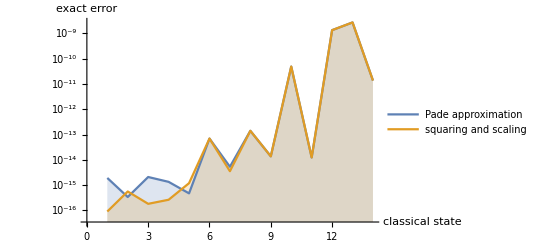

```mathematica
SSPadeClassAcu=ListLinePlot[{PadeClassErrorList,ssClassErrorList},Filling->Axis,PlotLegends->{"Pade approximation","squaring and scaling"},AxesLabel->{"classical state","exact error"},ScalingFunctions->"Log"]
```

```mathematica
Export[NotebookDirectory[]<>"EPS_figure\\SSPadeClassAcu.eps",SSPadeClassAcu]
```

C:\Users\mei\Desktop\Numerical methods\EPS_figure\SSPadeClassAcu.eps

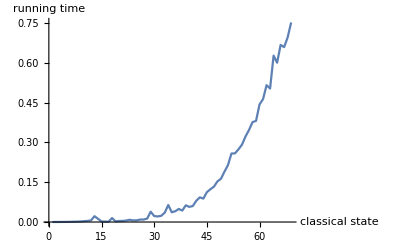

```mathematica
KryClassTime=ListLinePlot[KryClassTimeList,AxesLabel->{"classical state","running time"}]
```

```mathematica
Export[NotebookDirectory[]<>"EPS_figure\\KryClassTime.eps",KryClassTime]
```

C:\Users\mei\Desktop\Numerical methods\EPS_figure\KryClassTime.eps

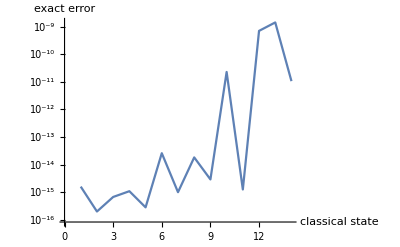

```mathematica
KryClassAcu=ListLinePlot[KryClassErrorList,AxesLabel->{"classical state","exact error"},ScalingFunctions->"Log"]
```

```mathematica
Export[NotebookDirectory[]<>"EPS_figure\\KryClassAcu.eps",KryClassAcu]
```

C:\Users\mei\Desktop\Numerical methods\EPS_figure\KryClassAcu.eps